NDSolve::ndsz: At t == -0.0254243, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0602823, step size is effectively zero; singularity or stiff system suspected.

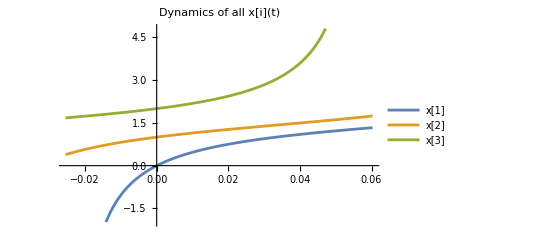

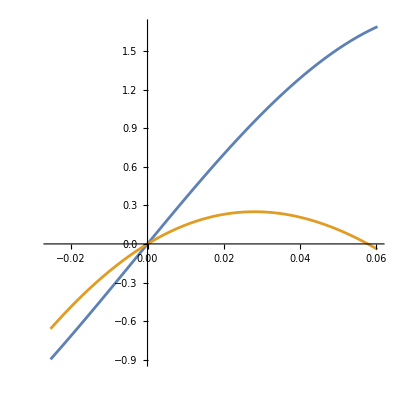
-Graphics-'

```mathematica
ClearAll["Global`*"]
(*Define the system of equations*)
u[k_,t_]:=Apply[Plus,Table[m[j][t](Exp[-Abs[x[k][t]-x[j][t]]]),{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t]Sign[k-j]Exp[-Abs[x[k][t]-x[j][t]]],{j,1,n}]]
u[k_,t_]:=Apply[Plus,Table[m[j][t](Abs[x[k][t]-x[j][t]]),{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[m[j][t]( (x[k][t]-x[j][t])/Abs[x[k][t]-x[j][t]]),{j,DeleteCases[Range[1,n],k]}]]

(*Define the number of equations*)
n=3; (*Example for n=5*)

(*Define initial conditions*)
initialConditions=Flatten[Table[{m[i][0]==RandomReal[{-2,2}],x[i][0]==RandomReal[{-2,2}]},{i,n}]];
initialConditions={
m[1][0]==1,x[1][0]==0,
m[2][0]==2,x[2][0]==1,
m[3][0]==3,x[3][0]==2
};

(*Define the system of ODEs*)
eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t]u[i,t],
x[i]'[t]==u[i,t]^2},
{i,n}
]];

(*Solve the system numerically*)
Tstart=-2;
Tend=10;
T={t,Tstart,Tend};
sol=NDSolve[Join[eqns,initialConditions],Flatten[Table[{m[i],x[i]},{i,n}]],T];
Tstart=Apply[Max,Table[sol[[1,i,2]]["Domain"][[1,1]],{i,1,2n}]];
Tend=Apply[Min,Table[sol[[1,i,2]]["Domain"][[1,2]],{i,1,2n}]];
T={t,Tstart,Tend};

plotM=Plot[Evaluate[Table[m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["m["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all m[i](t)",PlotStyle->Array[ColorData[97],n]];

plotX=Plot[Evaluate[Table[x[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]
GraphicsRow[{plotM,plotX}];

M1=m[1][0]^2+m[2][0]^2;
M2=m[1][0]m[2][0](x[2][0]-x[1][0]);
p[1]=ArcTan[m[2][0],m[1][0]];
p[2]=ArcTan[m[2][0],m[1][0]]+Pi/2;
mF[i_]:=Sqrt[M1]Sin[M2 t+p[i]];
xF[i_]:=-(M2/M1)(Cot[M2 t+p[i]]-Cot[p[i]])+x[i][0];
Plot[Evaluate[Table[m[i][t]-mF[i]/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]'
Plot[Evaluate[Table[x[i][t]-xF[i]/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1];

Plot[Evaluate[m[1][t]m[2][t]Abs[x[1][t]-x[2][t]]/.sol],T];
```

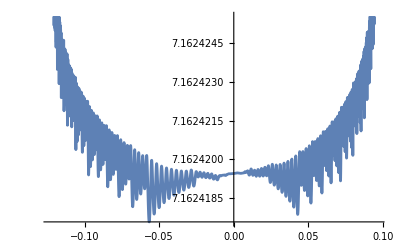

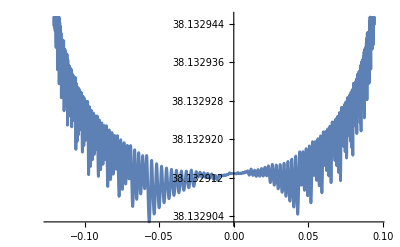

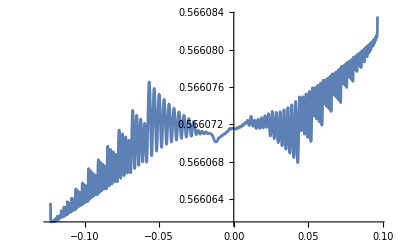

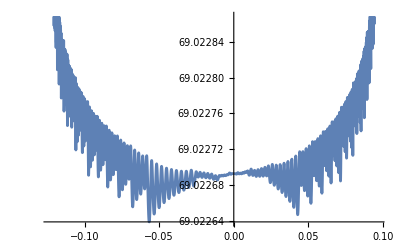

```mathematica
M1=(m[1][t]m[2][t]Abs[x[2][t]-x[1][t]])/.sol[[1]];
A1=m[1][t]^2(M1);
A2=m[2][t]^2(M1);
M3A=(A1 x[1][t]^0+A2 x[2][t]^0)/.sol[[1]];
M3B=(A1 x[1][t]^1+A2 x[2][t]^1)/.sol[[1]];
M3C=(A1 x[1][t]^2+A2 x[2][t]^2)/.sol[[1]];
plotX=Plot[Evaluate[M1],T]
plotX=Plot[Evaluate[M3A],T]
plotX=Plot[Evaluate[M3B],T]
plotX=Plot[Evaluate[M3C],T]
```

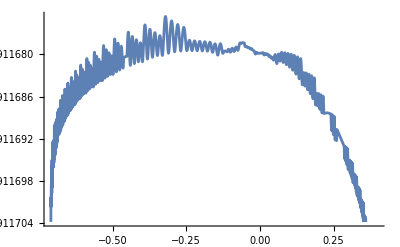

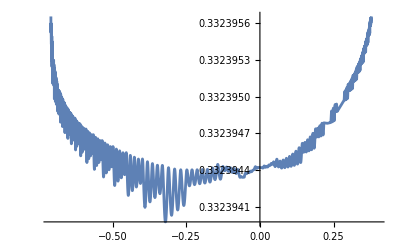

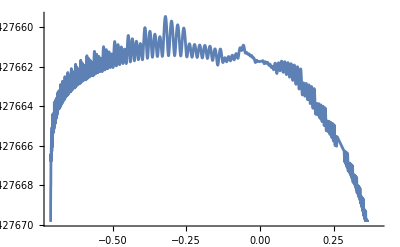

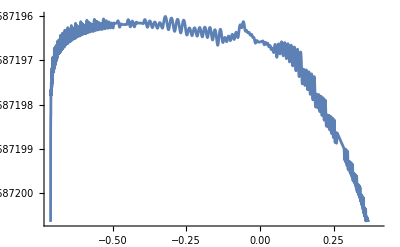

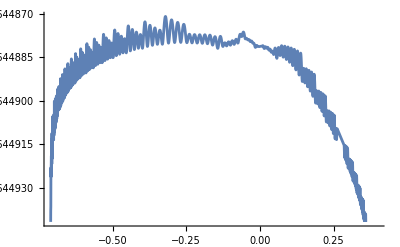

```mathematica
M1=(m[1][t]m[2][t]Abs[x[2][t]-x[1][t]]+m[1][t]m[3][t]Abs[x[3][t]-x[1][t]]+m[2][t]m[3][t]Abs[x[3][t]-x[2][t]])/.sol[[1]];
M2=(m[1][t]m[2][t]m[3][t])^2Abs[x[2][t]-x[1][t]]Abs[x[3][t]-x[1][t]]Abs[x[3][t]-x[2][t]]/.sol[[1]];
A1=m[1][t]^2(M1+2m[2][t]m[3][t]Abs[x[3][t]-x[2][t]]);
A2=m[2][t]^2(M1+2m[1][t]m[3][t]Abs[x[3][t]-x[1][t]]);
A3=m[3][t]^2(M1+2m[1][t]m[2][t]Abs[x[2][t]-x[1][t]]);
M3A=(A1 x[1][t]^0+A2 x[2][t]^0+A3 x[3][t]^0)/.sol[[1]];
M3B=(A1 x[1][t]^1+A2 x[2][t]^1+A3 x[3][t]^1)/.sol[[1]];
M3C=(A1 x[1][t]^2+A2 x[2][t]^2+A3 x[3][t]^2)/.sol[[1]];
plotX=Plot[Evaluate[M1],T]
plotX=Plot[Evaluate[M2],T]
plotX=Plot[Evaluate[M3A],T]
plotX=Plot[Evaluate[M3B],T]
plotX=Plot[Evaluate[M3C],T]

Mtest=x[2][t](m[1][t]^2+m[2][t]^2)-m[1][t]^2(x[2]-x[1])
plotX=Plot[Evaluate[M3C],T]
```